# Figure 7

#### Data

```mathematica
data1=Import["/home/daniel/Documents/Codigos/RabiModel/src/output/fidelities_adiabatic.dat"];
data2=Import["/home/daniel/Documents/Codigos/RabiModel/src/output/qfi_adiabatic.dat"];
data3=Import["/home/daniel/Documents/Codigos/RabiModel/src/output/negativity_adiabatic.dat"];
```

```mathematica
dat1=Table[{data1[[i,1]],data1[[i,2]]},{i,1,Length[data1]}];
dat2=Table[{data1[[i,1]],data1[[i,3]]},{i,1,Length[data1]}];
dat3=Table[{data2[[i,1]],data2[[i,2]]},{i,1,Length[data2]}];
dat4=Table[{data2[[i,1]],data2[[i,3]]},{i,1,Length[data2]}];
dat5=Table[{data3[[i,1]],data3[[i,2]]},{i,1,Length[data3]}];
```

#### Figure 7d

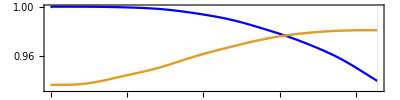

```mathematica
fig7d=Show[ListPlot[{dat1,dat2},Joined->True,
PlotStyle->{Blue,Thickness[0.0043]},PlotRange->All,GridLines->{{200*4.28},{}},GridLinesStyle->{{Red},{}},Frame->True,LabelStyle->{10,Black}],AspectRatio->0.25]
```

```mathematica
Export["protocol_fidelities.png",fig7d]
```

protocol_fidelities.png

#### Figure 7e

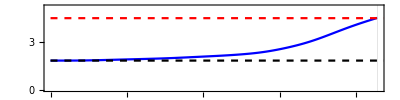

```mathematica
fig7e=Show[ListPlot[{dat3},Joined->True,
PlotStyle->{Blue,Thickness[0.0043]},PlotRange->{Automatic,{0,5.2}},GridLines->{{200*4.28},{}},GridLinesStyle->{{Red},{}},Frame->True,LabelStyle->{10,Black}],Plot[1.8283437968627987,{x,0,1100},PlotStyle->{Black,Dashed}],Plot[4.481004478220652,{x,0,1100},PlotStyle->{Red,Dashed}],AspectRatio->0.25]
```

```mathematica
Export["protocol_qfi.png",fig7e]
```

protocol_qfi.png

#### Figure 7f

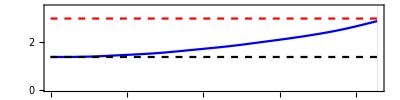

```mathematica
fig7e=Show[ListPlot[{dat4},Joined->True,
PlotStyle->{Blue,Thickness[0.0043]},PlotRange->{Automatic,{0,3.5}},GridLines->{{200*4.28},{}},GridLinesStyle->{{Red},{}},Frame->True,LabelStyle->{10,Black}],Plot[1.3821,{x,0,1100},PlotStyle->{Black,Dashed}],Plot[3,{x,0,1100},PlotStyle->{Red,Dashed}],AspectRatio->0.25]
```

```mathematica
Export["protocol_qfi.png",fig7e]
```

protocol_qfi.png

#### Figure 7g

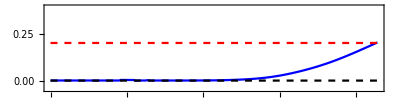

```mathematica
fig7e=Show[ListPlot[{dat5},Joined->True,
PlotStyle->{Blue,Thickness[0.0043]},PlotRange->{Automatic,{-0.05,0.4}},GridLines->{{250*4.28},{}},GridLinesStyle->{{Red},{}},Frame->True,LabelStyle->{10,Black}],Plot[0,{x,0,1100},PlotStyle->{Black,Dashed}],Plot[0.2036,{x,0,1100},PlotStyle->{Red,Dashed}],AspectRatio->0.25]
```

```mathematica
Export["protocol_qfi.png",fig7e]
```

protocol_qfi.png